{0.501057,Null}

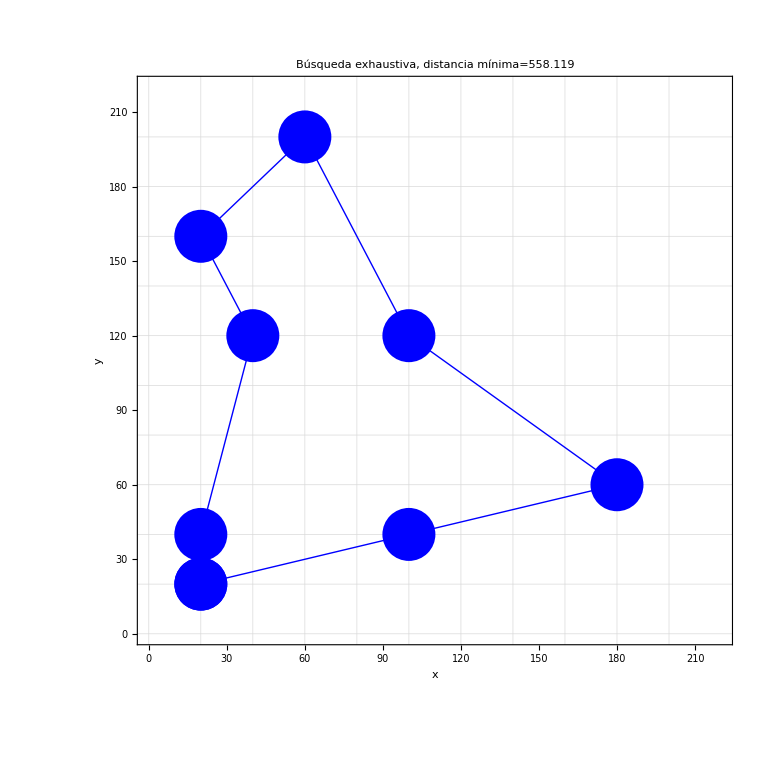

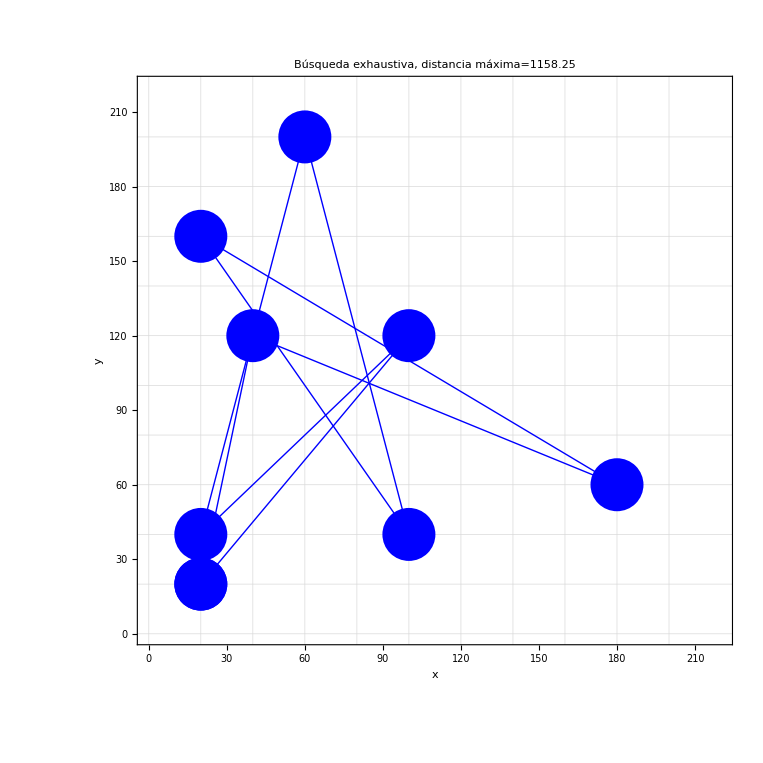

```mathematica
SetOptions[Graphics,
GridLines->{{0,20,40,60,80,100,120,140,160,180,200},{0,20,40,60,80,100,120,140,160,180,200}},
AspectRatio->1,
AxesOrigin->{0,0},Axes->True,
ImageMargins->{{10,15},{20,20}},
Frame->True,
FrameTicks->True,
PlotRange->{{0,220},{0,220}},
FrameLabel->{x,y},
ImageSize->{763,748}];

C1={20,20};
C2={60,20};
C3={160,20};
C4={20,40};
C5={100,40};
C6={200,40};
C7={180,60};
C8={60,80};
C9={120,80};
C10={180,100};
C11={40,120};
C12={100,120};
C13={140,140};
C14={20,160};
C15={100,160};
C16={200,160};
C17={80,180};
C18={140,180};
C19={60,200};
C20={180,200};

P1=Point[C1];
P2=Point[C2];
P3=Point[C3];
P4=Point[C4];
P5=Point[C5];
P6=Point[C6];
P7=Point[C7];
P8=Point[C8];
P9=Point[C9];
P10=Point[C10];
P11=Point[C11];
P12=Point[C12];
P13=Point[C13];
P14=Point[C14];
P15=Point[C15];
P16=Point[C16];
P17=Point[C17];
P18=Point[C18];
P19=Point[C19];
P20=Point[C20];

points2={C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,C13,C14,C15,C16,C17,C18,C19,C20};
map2={P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15,P16,P17,P18,P19,P20};

L1=Line[{C1,C2}];

distance[{x1_,y1_},{x2_,y2_}]:=Sqrt[(x2-x1)^2+(y2-y1)^2 ];

Timing[
perms=Permutations[{2,3,4,5,6,7,8}];  
For[i=1,i≤Length[perms],i++,perms[[i]]=Join[{1},perms[[i]],{1}]]; 

sample=RandomSample[Range[20],8];
sample=Join[sample,{sample[[1]]}];

Clist={};
For[i=1,i≤Length[sample],i++,Clist=Append[Clist,points2[[sample[[i]]]]]];
Plist={};
For[i=1,i≤Length[sample],i++,Plist=Append[Plist,map2[[sample[[i]]]]]] ;

distmax=0;
distmin=1000000;
caminomax;
caminomin;
dist=0;
For[i=1,i≤Length[perms],i++,
For[j=1,j≤Length[perms[[1]]]-1,j++,
dist+=distance[Clist[[perms[[i,j]]]],Clist[[perms[[i,j+1]]]]]
];
If[distmax<dist,distmax=dist;caminomax=perms[[i]]];
If[distmin>dist,distmin=dist;caminomin=perms[[i]]];
dist=0;
];]

Llistmin={};
For[i=1,i≤Length[Clist]-1,i++,Llistmin=Append[Llistmin,Line[{Clist[[caminomin[[i]]]],Clist[[caminomin[[i+1]]]]}]]
];
Framed[Graphics[{PointSize[0.05],Blue,Plist,Llistmin},PlotLabel->Text[Style[TemplateApply["Búsqueda exhaustiva, distancia mínima=``",1.0*distmin],20,Black]]]]

Llistmax={};.
For[i=1,i≤Length[Clist]-1,i++,Llistmax=Append[Llistmax,Line[{Clist[[caminomax[[i]]]],Clist[[caminomax[[i+1]]]]}]]
];
Framed[Graphics[{PointSize[0.05],Blue,Plist,Llistmax},PlotLabel->Text[Style[TemplateApply["Búsqueda exhaustiva, distancia máxima=``",1.0*distmax],20,Black]]]]
```

```mathematica
]
```

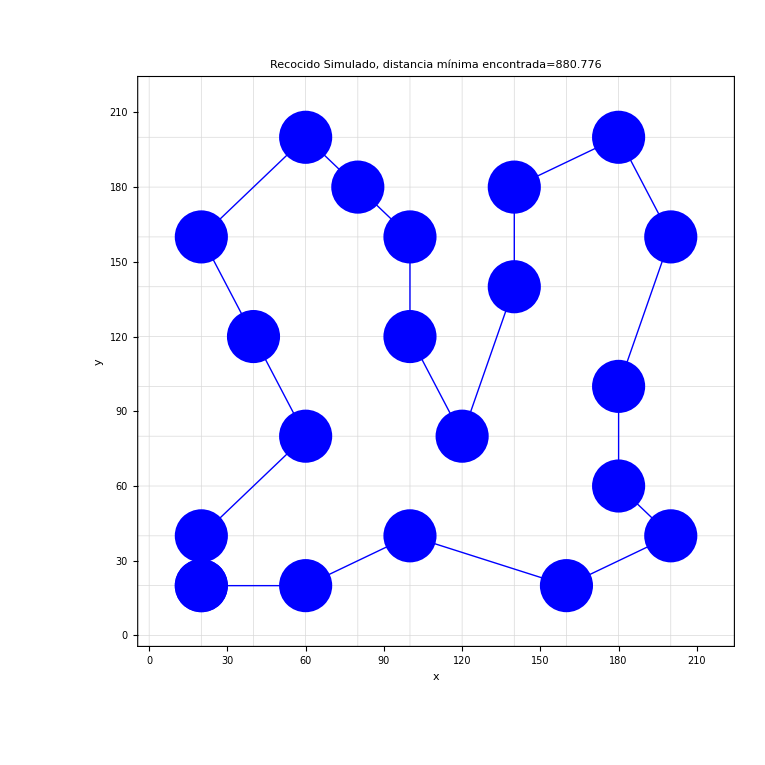

```mathematica
(*Recocido simulado*)

dmin=10000000;
dmax=0;

s0={C1,C2,C3,C4,C5,C6,C7,C8,C9,C10,C11,C12,C13,C14,C15,C16,C17,C18,C19,C20,C1};(*Clist;*)

(*Aleatorizar vector inicial*)
SeedRandom[];
For[i=1,i≤10000,i++,
aux1=RandomInteger[{2,Length[s0]-1}];
aux2=RandomInteger[{2,Length[s0]-1}];
aux3=s0[[aux1]];
s0[[aux1]]=s0[[aux2]];
s0[[aux2]]=aux3
];

s=s0;
snew;
T=10000;
P[s_,snew_,T_]:=Exp[-(snew-s)/(0.01*T)];
distance[{x1_,y1_},{x2_,y2_}]:=Sqrt[(x2-x1)^2+(y2-y1)^2 ];
numelems=Length[s];
distS=0;
distSnew=0;
distmax=0;
distmin=1000000;
caminomax;
caminomin;
movieVector={};

Plist={};
For[i=1,i≤Length[s],i++,Plist=Append[Plist,Point[s[[i]]] ]];

Monitor[

While[T>0,
(*-----------------Calcular snew---------------*)
n=RandomInteger[{2,numelems-2}];
place=RandomInteger[{0,numelems-2-n}];
pathToReverse={};
pathBefore={};
pathAfter={};

For[i=0,i≤n-1,i++,pathToReverse=Append[pathToReverse,s[[2+place+i]]]];
pathToReverse=Reverse[pathToReverse];

For[i=1,i≤2+place-1,i++,pathBefore=Append[pathBefore,s[[i]]]];
For[i=2+place+n,i≤Length[s],i++,pathAfter=Append[pathAfter,s[[i]]]];

snew=Join[pathBefore,pathToReverse,pathAfter];
(*--------------------------------------------*)

For[j=1,j≤Length[s]-1,j++,
distS+=distance[s[[j]],s[[j+1]]];
distSnew+=distance[snew[[j]],snew[[j+1]]]
];

If[distmax<distSnew,distmax=distSnew;caminomax=snew];
If[distmin>distSnew,distmin=distSnew;caminomin=snew];

If[RandomReal[{0,1}]<1.0*P[distS ,distSnew,T]||distSnew<distS,s=snew];

T-=1;
distS=0;
distSnew=0;

Llistmin={};
For[i=1,i≤Length[s]-1,i++,Llistmin=Append[Llistmin,Line[{s[[i]],s[[i+1]]}]]];

grafica=Framed[Graphics[{PointSize[0.05],Blue,Plist,Llistmin},PlotLabel->Grid[Table[Text[Style[TemplateApply["Recocido Simulado, distancia mínima encontrada=``",1.0*distmin],20,Black]],{1},{1}],Frame->True,Spacings->{7.5,3}]]];
If[T==9999 || T==0,Pause[3]];
If[Mod[T+1,50]==0 || T==9999, AppendTo[movieVector,grafica]]
];
,grafica];
grafica
```

```mathematica
(*Distancia máxima*)
Llistmax={};
For[i=1,i≤Length[s]-1,i++,Llistmax=Append[Llistmax,Line[{caminomax[[i]],caminomax[[i+1]]}]]
];
Framed[Graphics[{PointSize[0.05],Blue,Plist,Llistmax},PlotLabel->Grid[Table[Text[Style[TemplateApply["Recocido Simulado, distancia máxima=``",1.0*distmax],20,Black]],{1},{1}],Frame->True,Spacings->{7.5,3}]]]
```

```mathematica
(*Guardar video*)

fileName1="./Desktop/recocidoSimuladoMathematica1.avi";
Export[fileName1,movieVector];
```